# Assignment 3, Part 2

## Optimization in 1D

```mathematica
SetDirectory["C:\\Users\\brook\\Documents\\Workspaces\\CSC 450\\CSC450\\assignment3"]
FileNames[]
```

C:\Users\brook\Documents\Workspaces\CSC 450\CSC450\assignment3

{a3_notebook.nb,a3_p1_f1_1D.csv,a3_p1_f1.csv,a3_p1_f1_ground.csv,a3_p1_f2_1D.csv,a3_p1_f2.csv,a3_p1_f2_ground.csv,a3_p1_f3.csv,a3_p1_f4.csv,a3_p1_f5_1D.csv,a3_p1_f5.csv,a3_p1_f5_ground.csv,a3_p1_f6.csv,Mathematica.md,output1_b.csv,output3_f10.csv,output3_f11.csv,output3_f12.csv,output3_f6.csv,output3_f7.csv,output3_f8.csv,output3_f9.csv,output3_p4_1.csv,output3_p4_2.csv,output3_p4_3.csv,output3_p4_4.csv,output3_p4_5.csv,output3_p4_a.csv,output3_p4_b.csv,output3_p4_c.csv,output3_p4_d.csv,output3_p4_e.csv,output3_p4_f.csv,output3_p4_g.csv}

## Steepest Descent

### Example 1

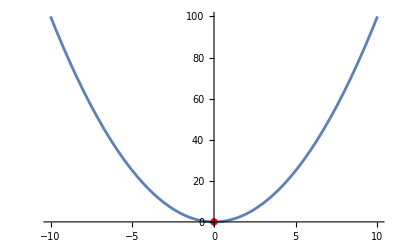

```mathematica
data3a=Import["output3_f1.csv","CSV"];
f[x_]:=x^2;
Show[ListPlot[data3a,PlotStyle->Red],Plot[f[x],{x,-10,10}],PlotRange->All]
```

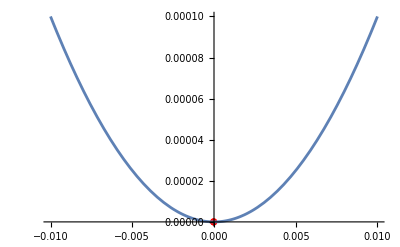

```mathematica
Show[ListPlot[data3a,PlotStyle->Red],Plot[f[x],{x,-0.01,0.01}],PlotRange->All]
```

The naive steepest descent algorithm correctly identified the minimum of this very simple function. It correctly defined ~ x = 0 as the minimum using a delta X of 0.01 and a tolerance of 0.001. It took 500 iterations.

### Example 2

Given this more complicated function, we can use different starting points to find different minima.

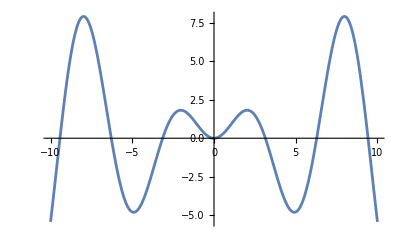

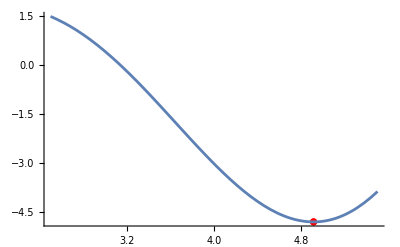

```mathematica
data3b=Import["output3_f2.csv","CSV"];
g[x_]:=x*Sin[x]
Plot[g[x], {x,-10,10}]
Show[ListPlot[data3b,PlotStyle->Red],Plot[g[x],{x,2.5,5.5}],PlotRange->All]
```

Starting at X = 3, it finds a minimum at ~4.91. This was not successful, however, because it did not fall within the tolerance of 0.001. 

I tried using a delta X of 0.01 to start and then tried increasing the precision to 0.001, which took 1913 iterations to reach (4.9128613,-4.8144693).

We can find another min starting with X = -1.2.

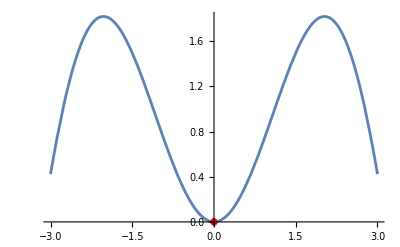

```mathematica
data3b=Import["output3_f3.csv","CSV"];
Show[ListPlot[data3b,PlotStyle->Red],Plot[g[x],{x,-3,3}],PlotRange->All]
```

## GSS

### Example 1

```mathematica
data3a=Import["output3_f4.csv","CSV"];
f[x_]:=x^2;
```

```mathematica
Show[ListPlot[data3a,PlotStyle->Red],Plot[f[x],{x,-0.01,0.01}],PlotRange->All]
```

-Graphics-

Establishing a baseline with this algorithm compared to the steepest descent one. 
It correctly defined x = 0 as the minimum using the same tolerance of 0.001. It took 20 iterations while the steepest descent took 500 using a delta X of 0.01.

### Example 2

Also trying GSS on the more complex function.

```mathematica
data3b=Import["output3_f5.csv","CSV"];
g[x_]:=x*Sin[x]
Plot[g[x], {x,-10,10}]
Show[ListPlot[data3b,PlotStyle->Red],Plot[g[x],{x,-3,3}],PlotRange->All]
```

-Graphics-

-Graphics-

Within bounds [-2, 2], the GSS algorithm was successful, finding a minimum ~ x = 0, unlike steepest descent before, falling within the required tolerance. It took 17 iterations instead of just under 2,000 before.

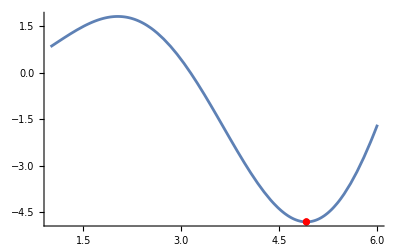

```mathematica
data3b=Import["output3_f6.csv","CSV"];
Show[ListPlot[data3b,PlotStyle->Red],Plot[g[x],{x,1,6}],PlotRange->All]
```

This also took 17 iterations, finding the minimum at (4.9132614, -4.81447).

## Parabolic Approximation

### Example 1

```mathematica
data3b=Import["output3_f7.csv","CSV"];
g[x_]:=x*Sin[x]
Plot[g[x], {x,-10,10}]
Show[ListPlot[data3b,PlotStyle->Red],Plot[g[x],{x,-3,3}],PlotRange->All]
```

-Graphics-

-Graphics-

Within bounds [-2, 2], the parabolic approximation was successful, finding a minimum x = 0. It found the minimum after only 1 iteration, which makes sense because this function has many parabolic segments, 
so it’s able to easily match a parabola given its range and the way x1, x2, and x3 are computed.

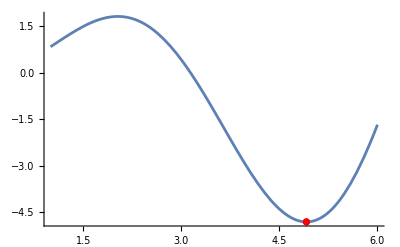

```mathematica
data3b=Import["output3_f8.csv","CSV"];
Show[ListPlot[data3b,PlotStyle->Red],Plot[g[x],{x,1,6}],PlotRange->All]
```

Like  the  last  two  algorithms, the  next  test  is  in  the  range  of [1, 6] . It  successfully  found  the  minimum  at [.913069, -4.81447]  over  7  iterations  which  makes  the  parabolic  
approximation  the  best  for  this  function  out  of  the  3  tried .

### Example 2

Now, I’m going to compare the results of GSS and parabolic approximation on a new function that won’t be as easy for parabolic approximation.

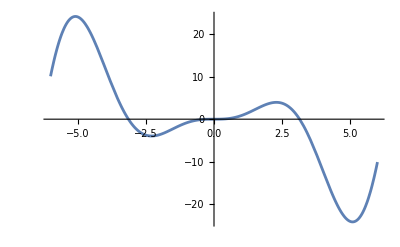

```mathematica
g[x_]:=x^2*Sin[x]
Plot[g[x], {x,-6,6}]
```

#### With parabolic approximation

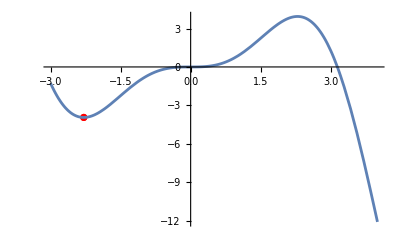

```mathematica
data3b=Import["output3_f9.csv","CSV"];
Show[ListPlot[data3b,PlotStyle->Red],Plot[g[x],{x,-3,4}],PlotRange->All]
```

With parabolic approximation, it correctly found the minimum in the provided range [-4, 3] at (-2.287934, -3.9452977) and it took 10 iterations. Each example maintains a tolerance of 0.001.

In another range [-1, 6] it found another minutum at (1.0000159, 0.84150624). This took 37 iterations. Since this range technically has 2 minimums, due to the implementation, it chose the one closer to x = 0.

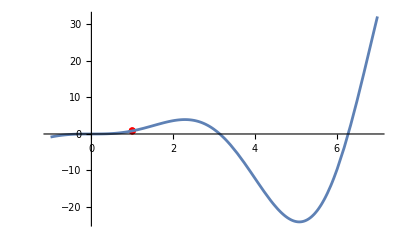

```mathematica
data3b=Import["output3_f10.csv","CSV"];
Show[ListPlot[data3b,PlotStyle->Red],Plot[g[x],{x,-1,7}],PlotRange->All]
```

#### With GSS

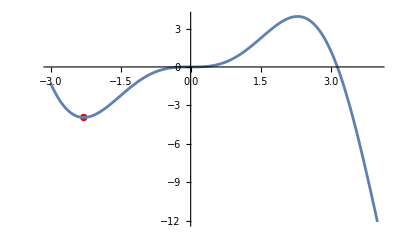

```mathematica
data3b=Import["output3_f11.csv","CSV"];
Show[ListPlot[data3b,PlotStyle->Red],Plot[g[x],{x,-3,4}],PlotRange->All]
```

GSS also correctly found the minimum within the range of [-4, 3] with identical precision, but it took 19 iterations. Both performed well here--better than the steepest descent approach.

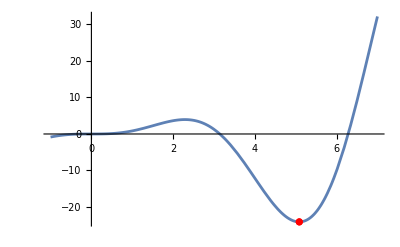

```mathematica
data3b=Import["output3_f12.csv","CSV"];
Show[ListPlot[data3b,PlotStyle->Red],Plot[g[x],{x,-1,7}],PlotRange->All]
```

Conversely, to the second range using the parabolic approximation, GSS, due to its implementation differences, chose the minimum at (5.087039, -24.08296), taking 19 iterations.